```mathematica
Clear[bulkEdgeFunctionFor1DRibbon]
bulkEdgeFunctionFor1DRibbon[ribbonprimitivecell0:{{__}..}|{Rule[_,{__}]..},veclongi:{_,_}(*|{_,_,_}*),innerdof_Integer:2,n_:3]:=Module[{dim=Length[veclongi],ϕ,coordstrans,rottransf,innerid,diaglis,diagmat,pts,signedpower},
signedpower[i_]:=If[OddQ[i],1,Sign[#]]#^i&;
pts=If[FreeQ[Rule][#],#,Values[#]]&[ribbonprimitivecell0];
ϕ=ArcTan@@veclongi;rottransf=RotationTransform[ϕ];
coordstrans=rottransf[pts][[;;,2]];
(*diaglis=Standardize[coordstrans,Mean,1/2 #&@*Norm@*MinMax];*)
diaglis=signedpower[n][Rescale[coordstrans,MinMax[coordstrans],{-1.,1.}]];
diagmat=DiagonalMatrix[diaglis,TargetStructure->"Sparse"];
innerid=IdentityMatrix[innerdof,SparseArray];
KroneckerProduct[diagmat,innerid]
];

Clear[ribbonBulkBoundaryOperator]
ribbonBulkBoundaryOperator[ribbonprimitivecell0:{{__}..}|{Rule[_,{__}]..},vecnorm:{_,_}|{_,_,_},innerdof_Integer:2,n_:3]:=Module[{nd=Normalize[vecnorm],ϕ,coordstrans,rottransf,innerid,diaglis,diagmat,pts,signedpower},
signedpower=Sign[#]Abs[#]^n&;
pts=If[FreeQ[Rule][#],#,Values[#]]&[ribbonprimitivecell0];
coordstrans=pts.nd;
diaglis=signedpower[Rescale[coordstrans,MinMax[coordstrans],{-1.,1.}]];
diagmat=DiagonalMatrix[diaglis,TargetStructure->"Sparse"];
innerid=IdentityMatrix[innerdof,SparseArray];
KroneckerProduct[diagmat,innerid]
];
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

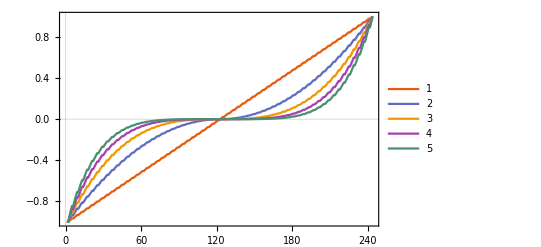

```mathematica
ribbonBulkBoundaryOperator[cryststruct1dzz[[1]],{0,1},1,#]&/@{1,2,3,4,5}
ListLinePlot[Diagonal/@%,(*PlotMarkers->"OpenMarkers",*)PlotRange->All,PlotLegends->Automatic]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

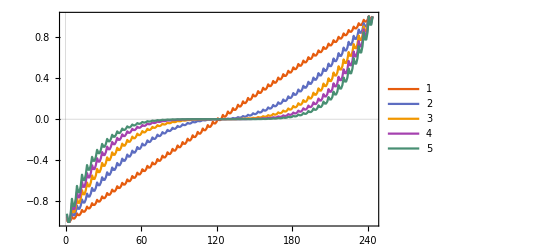

```mathematica
ribbonBulkBoundaryOperator[cryststruct1dac[[1]],{1,0},1,#]&/@Range[5]
ListLinePlot[Diagonal/@%,(*PlotMarkers->"OpenMarkers",*)PlotRange->All,PlotLegends->Automatic]
```